```mathematica
1/Integrate[ Exp[- m / (2 k T ) (x^2+ y^2+z^2)],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{x∈Reals,y∈Reals,T>0,m>0,k>0}]
```

1/(2 √2 π^(3/2) ((k T)/m)^(3/2))

(ⅇ^(-(m (x^2+y^2))/(2 k π T)) π (x^2+y^2))/((Assumptions→{x∈ℝ,y∈ℝ,T>0,m>0,k>0})[ⅇ^(-(m (x^2+y^2))/(2 k π T)) π (x^2+y^2)])

```mathematica
vbar=0.5;
```

```mathematica
normMax[vb_,v_]:=1/(√π)Exp[-(v-vb)^2]
normMaxHeavy[vb_,v_]:=1/(√π)Exp[-(v-vb)^2] UnitStep[v]
```

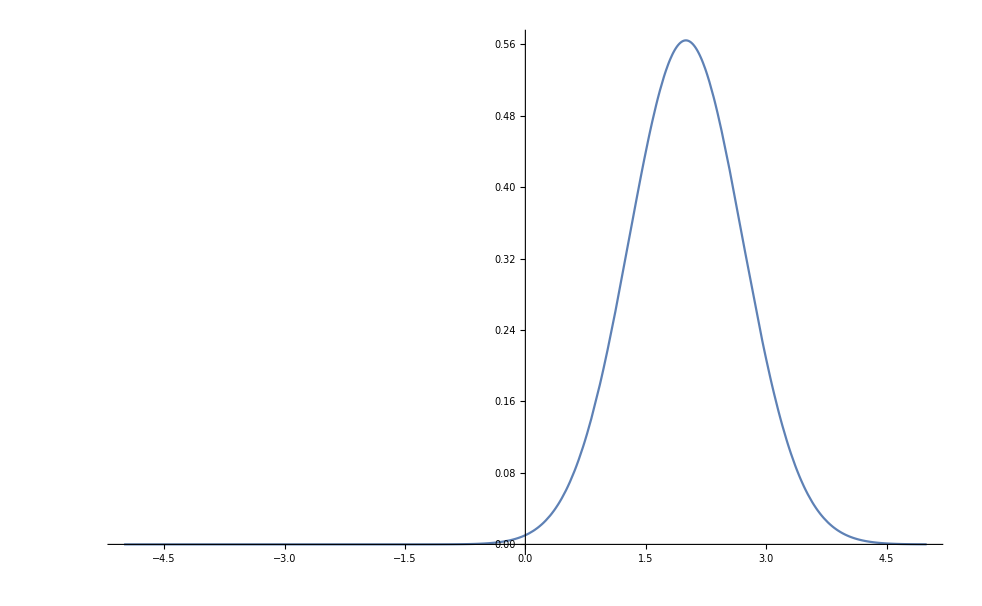

```mathematica
Plot[normMax[2,v],{v,-5,5}]
```

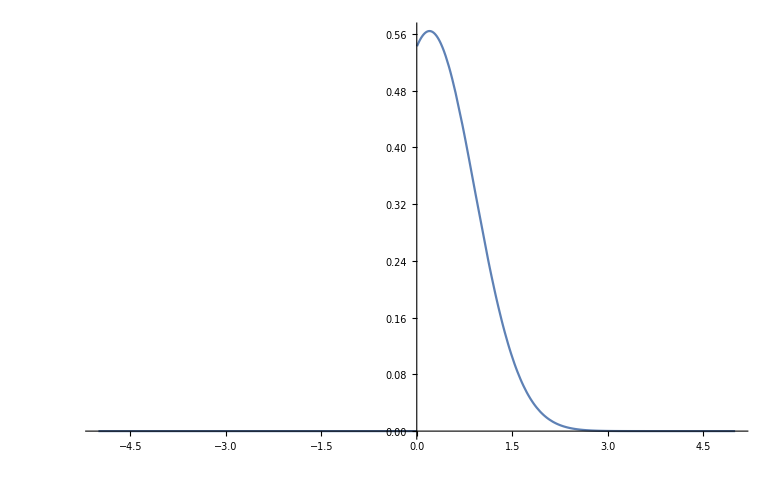

```mathematica
Plot[normMaxHeavy[0.2,v],{v,-5,5},PlotRange->{Full,Full}]
```

## Barbosa 2-D func

```mathematica
barbDist[vz_,vperp_,V_,alpha_]:=Exp[-(vz^2+vperp^2+V^2-2V (vz^2+ vperp^2 (1 - alpha) )^(1/2))] UnitStep[vz]
```

## α = 1 (no mirroring, so vanilla Maxwellian)

```mathematica
Plot3D[barbDist[vz,vperp,2,1],{vz,0,5},{vperp,-2.5,2.5},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[barbDist[vz,vperp,5,0.0],{vz,0,8},{vperp,-4,4},PlotRange->All]
```

-Graphics3D-